```mathematica
Clear["Global`*"];
```

```mathematica
a=100;
```

```mathematica
pA={2*a,0};pB={0,2*a};pC={a,0};pD={0,a};
```

```mathematica
pE={2*a-t,t}
```

{200-t,t}

```mathematica
pO1={3*a/2,y};
Solve[EuclideanDistance[pA,pO1]==EuclideanDistance[pE,pO1],y]
```

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

{{y→(-2500+t^2+Abs[50-t]^2)/(2 t)}}

```mathematica
pO1={3*a/2,(-2500+t^2+(50-t)^2)/(2 t)}//FullSimplify
r1=EuclideanDistance[pA,pO1]
```

{150,-50+t}

√(2500+Abs[50-t]^2)

```mathematica
C1=(x-150)^2+(y-(t-50))^2==2500+(t-50)^2
```

(-150+x)^2+(50-t+y)^2==2500+(-50+t)^2

```mathematica
pO2={x,3*a/2};
Solve[EuclideanDistance[pB,pO2]==EuclideanDistance[pE,pO2],x]
```

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

{{x→(-37500+400 t-t^2-Abs[-150+t]^2)/(2 (-200+t))}}

```mathematica
pO2={(-37500+400 t-t^2-(-150+t)^2)/(2 (-200+t)),3*a/2}//FullSimplify
rw=EuclideanDistance[pB,pO2]
```

{150-t,150}

√(2500+Abs[-150+t]^2)

```mathematica
C2=(x-(150-t))^2+(y-150)^2==2500+(t-150)^2
```

(-150+t+x)^2+(-150+y)^2==2500+(-150+t)^2

```mathematica
solF=Solve[C1&&C2,{x,y}]
```

{{x→200-t,y→t},{x→-(10000 (-200+t))/(20000-200 t+t^2),y→(10000 t)/(20000-200 t+t^2)}}

```mathematica
pF={x,y}/.solF[[2]]
```

{-(10000 (-200+t))/(20000-200 t+t^2),(10000 t)/(20000-200 t+t^2)}

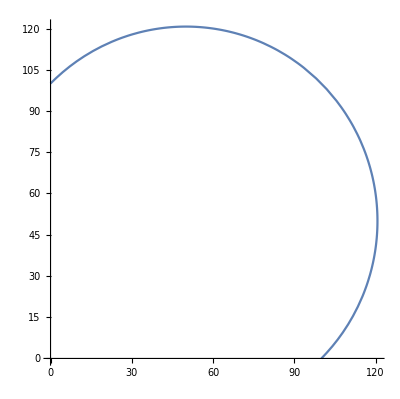

```mathematica
ParametricPlot[pF,{t,0,2*a}]
```

```mathematica
xt=pF[[1]];yt=pF[[2]];
```

```mathematica
s=Integrate[Sqrt[D[xt,t]^2+D[yt,t]^2],{t,0,2*a}]
```

50 √2 π

```mathematica
Print[Floor[s]]
```

222